# Twine Story Taxonomy

## Features

Twine is used for creating Interactive Stories (aka Interactive Fiction) and Text-Based Games.

### Passages

#### Link to Passages

Simple Link

[[Open the cage door]]

Hidden Link (implement later)

[[Open the cage door | Devoured By Lions]]

Link Reference

#### Styling

Markdown style support

Style Reference

#### Random Events

The referee reveals that the coin is (either:”heads”,”tails”).

Randomness Reference

#### Custom HTML

### Features for later

#### Inventory

Inventory Reference

#### Multimedia Embedding

Multimedia Reference

## Structure

Twine Story : Network of Passages

Passage : Text interspersed with Links to other nodes,  Random Events, State Saving

## Layout

Make use of the WL graph Layout options to specify the positions of passages on export.

## Exploring A Story

GUI for exploring the story

Display one passage at a time

Clicking a link in a passage will display the linked passage

Play, Stop, Go Back etc..

Use Dynamic? and update a value named currentPassage?

1 | Display first passage

2 | Click on a link in the passage to display that passage.

A Basic Mock Up below: However, in practice one will click the links to get to the next passage.

```mathematica
Manipulate[currentPassage, {currentPassage,Table[Framed[Column[{"PassageName " <> ToString[i],Framed["This is Passage Content "<>ToString[i - 1] <> ". And a link to passage [[" <> ToString[i ]<>"]]"]}]], {i, 5}] }, ControlType->SetterBar]
```

### Custom Interface Construction

Custom Interface Construction Reference

Make use of Dynamic Module probably

Low level Interface control

Event Handler

#### Here’s a good starting example

```mathematica
DynamicModule[{col=Green},EventHandler[Style["text",FontColor->Dynamic[col]],{"MouseClicked":>(col=col/.{Red->Green,Green->Red})}]]
```

The change I need to make:  col = Green ⇒ col = passage

```mathematica
linkedPassage = "Linked Passage";
```

```mathematica
DynamicModule[{currentpassage="First Passage"},EventHandler[Dynamic[currentpassage],{"MouseClicked":>(currentpassage= linkedPassage)}]]
```

#### Another example

```mathematica
DynamicModule[{p={0,0},c=Green},EventHandler[EventHandler[Framed@Dynamic[Graphics[{c,Disk[p,0.2]},PlotRange->2]],{"MouseDown":>(c=c/.{Red->Green,Green->Red})}],{"MouseDown":>(p=MousePosition["Graphics"])},PassEventsDown->True]]
```

#### Text Case

If a  in a passage is clicked, display the passage the link goes to.

```mathematica
test =Framed[Row[{"Go to this ", Button[Style["Link", Blue, Bold],"Next Passage", Appearance->None]}]]
```

Go to this Link

Christopher Suggested using Button in Row

```mathematica
DynamicModule[{currentpassage= test },
currentpassage =Framed@Row[
{"Go to this ", 
Button[Style["Link", "Hyperlink", Bold],currentpassage=Framed@"Welcome To Next Passage, go here next" , Appearance->None]}];
Dynamic[currentpassage]
]
```

```mathematica
Row[{"Welcome to the Next Passage, go ", Button[Style["here", "Hyperlink", Bold],,Appearance -> None], " next."}]
```

Welcome to the Next Passage, go here next.

The idea here is that we control the movement, or display of the vertex, through the graph. We only display the content of one node at a time.

I think the following code is good, now I need to generalize it.

DynamicModule[{currentpassage = test },
currentpassage = Framed@Row[
{“Go to this “, 
Button[Style[“Link”, “Hyperlink”, Bold],
currentpassage = Framed@”Welcome To Next Passage, go here next”, 
Appearance→None]}];
Dynamic[currentpassage]
]
 
 To do this, each passage needs to be converted into a row. (side-question: One row with all the content?
 
DynamicModule[{currentpassage = <first-passage> },
currentpassage = Framed@Row[
{“Go to this “, 
Button[Style[“Link”, “Hyperlink”, Bold],
currentpassage = Framed@”Welcome To Next Passage, go here next”, 
Appearance→None]}];
Dynamic[currentpassage]
]

#### Defining a Wolfram Language Twine Story Grammar

It will be useful to define a grammar, for two reasons:
(1) Understand story structure
(2) Framework for building an Interpreter

The Grammar:

Story             → PassageExpression
PassageExpression → Passage | Passage .. 
Passage           → StringExpression | StringExpression .. 
StringExpression  → WordSequence | WordSequence Link WordSequence
WordSequence      → WhiteSpace Word WhiteSpace | WhiteSpace Word WhiteSpace ..
Link              → [[ LinkName ]]
LinkName          → WordSequence

Grammar Rules Reference

Try an example

Doesn’t work without CloudDeploy

```mathematica
customG =GrammarRules[{FixedOrder["add", a:GrammarToken["SemanticNumber"], "and", b:GrammarToken["SemanticNumber"]] :> a + b}
]
```

GrammarRules[{FixedOrder[add,a:GrammarToken[SemanticNumber],and,b:GrammarToken[SemanticNumber]]:>a+b}]

```mathematica
GrammarApply[customG, "add six and seven"]
```

GrammarApply::arg1: The first argument GrammarRules[{FixedOrder[add,a:GrammarToken[SemanticNumber],and,b:GrammarToken[SemanticNumber]]:>a+b}] is expected to be a CloudObject or list of CloudObject.

GrammarApply[GrammarRules[{FixedOrder[add,a:GrammarToken[SemanticNumber],and,b:GrammarToken[SemanticNumber]]:>a+b}],add six and seven]

I want to Define GrammarRules locally, so that I don’t need to use cloud credits
Here’s what it looks like with Cloud Functions

```mathematica
customG2 =CloudDeploy[GrammarRules[{FixedOrder["add", a:GrammarToken["SemanticNumber"], "and", b:GrammarToken["SemanticNumber"]] :> a + b}]]
```

CloudObject[https://www.wolframcloud.com/objects/0164448d-c34c-40ef-8305-661f83b20b43]

```mathematica
GrammarApply[customG2, "add six and seven"]
```

13

#### Standalone interfaces

Standalone interface reference

#### Story Explorer

Wrap the vertices of the graph with Buttons: the buttons, when clicked show the active passage

The left graphic should display the button.

```mathematica
activePassage = 0
```

0

```mathematica
b =Button[2, activePassage = "Passage Two"];
```

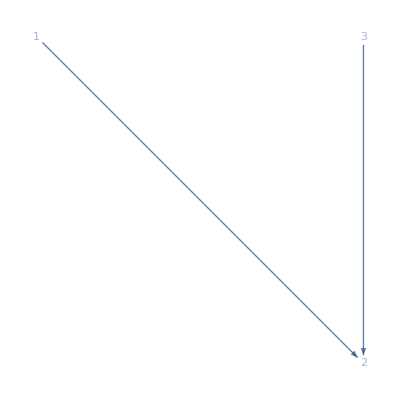

```mathematica
GraphicsRow[{Dynamic[Framed@activePassage],Graph[{Button[1,activePassage = "Passage One" ]->b, Button[3, activePassage = "Passage Three"] -> b}, VertexShapeFunction->"Name"]}]
```

Procedure | Generate a list of buttons for each passage of the form:
Button[<PassageName>, activePassage = <PassageContent>]